```mathematica
resultados=Import["./valores_eduardo.dat","Table"]//ToExpression;
```

```mathematica
resultados//Dimensions
```

{40,12}

```mathematica
Import["/home/david/pro7/libs/QuantumDavid.m"]
```

```mathematica
campo=linearmesh[0,Pi/2,40];
```

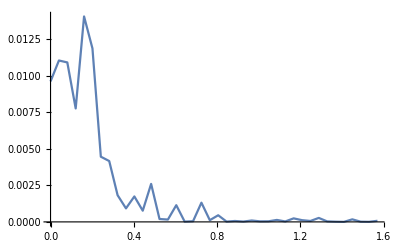

```mathematica
ListLinePlot[Table[{campo[[k]],resultados[[k]][[1]]},{k,1,40}]]
```

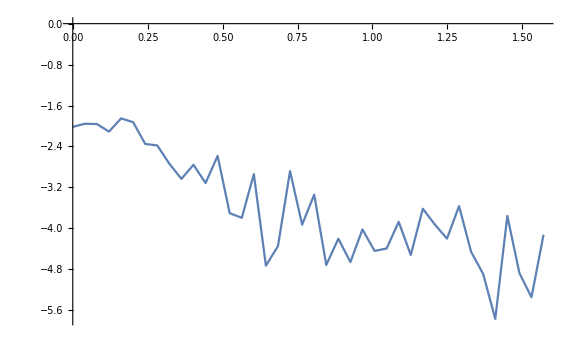
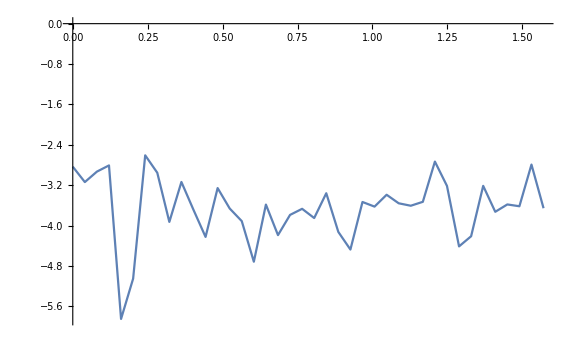
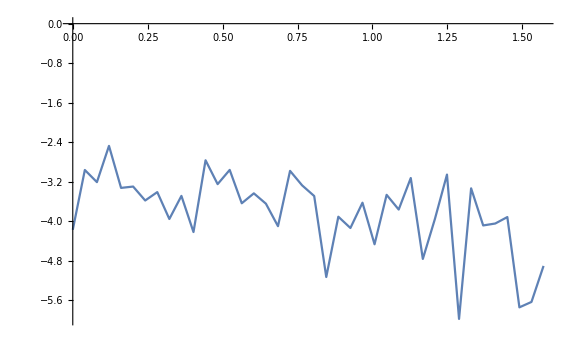
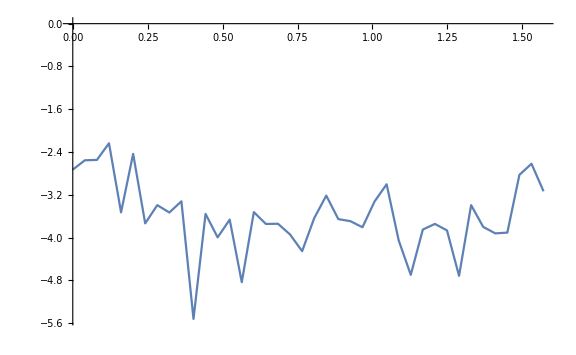
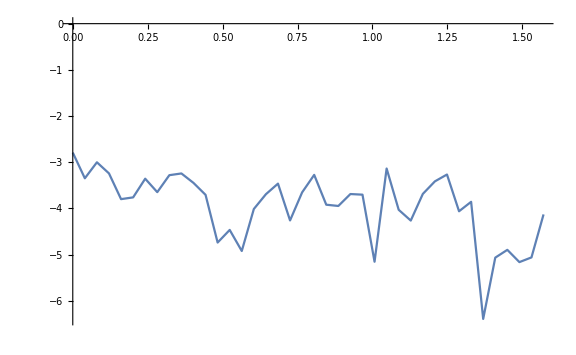
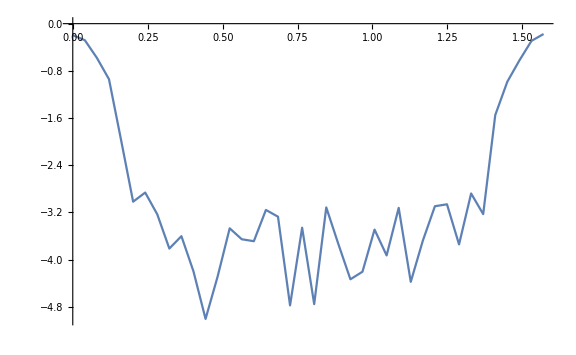
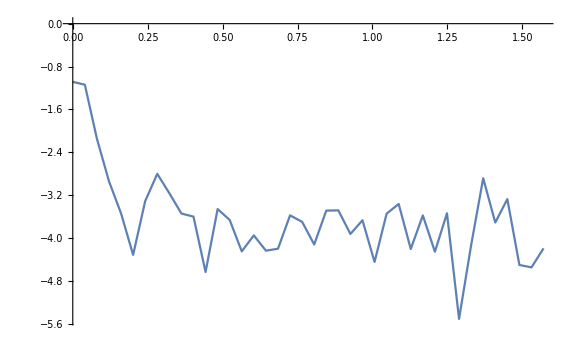
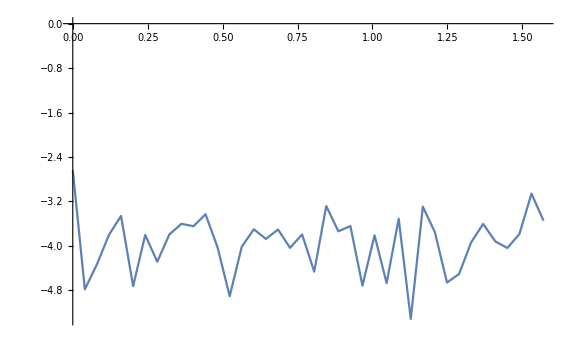

```mathematica
Table[ListLinePlot[Table[{campo[[k]],Log[10,resultados[[k]][[i]]]},{k,1,40}],ImageSize->Large],{i,1,12}]
```